```mathematica
u0=1.*10^-8;α=0.1;a=0.1;V[r_]=-α/r;δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);
Veff[c_][r_]=-α/r Erf[r/(√2 a)]+c a^2 δa[r];m=1.;l=0;l1=-1/2+√((l+1/2)^2-(α)^2);
k:=√((e+m)^2-m^2);γ:=(*(√(k^2+m^2) α)/k*)(α m)/k;
r2=u0;
r1=50.;
```

```mathematica
WList={10^-10,10^-5,.001,.003,.007,.01,.03,.07,.1,.3,.7,1};
```

```mathematica
Flatten@Map[{
e=#;
sol1=First@NDSolve[{-f''[x]+2m V[x]f[x]-(e-V[x])^2/4 f[x]==2m e f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{f[r2]==u0,f'[r2]==1}}];
δs1=FindRoot[(f'[r1] ((e-V[r1])/(8 m)+1)-(f[r1] V'[r1])/(8 m))/((1+(e-V[r1])/(8m))f[r1])==(k+1/(k r1)) Cot[k r1+δ](*(k+1/(k r1))Cot[k r1 -(l1 π)/2+γ Log[2k r1]+δ]*)/.sol1,{δ,0.7}]; 
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&]}&,WList]//AbsoluteTiming
```

NDSolve::precw: 参数函数的精度 ({-1/4 (1/10000000000 + Times[« 2 »])^2 f[x] - 0.2` f[x]/x - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({-1/4 (1/100000 + Times[« 2 »])^2 f[x] - 0.2` f[x]/x - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({-1/4 (0.001`  + Times[« 2 »])^2 f[x] - 0.2` f[x]/x - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve :: precw 的进一步输出将被抑制.

{1.41472,{1.57014,1.3637,0.034036,0.479578,-0.950779,-1.04952,1.53945,0.945803,0.592755,-1.44436,-0.299386,1.44504}}

```mathematica
e=10^-10;
sol1=First@NDSolve[{-f''[x]+2m V[x]f[x]-(e-V[x])^2/4 f[x]==2m e f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{f[r2]==u0,f'[r2]==1}}];
δs1=FindRoot[(f'[r1] ((e-V[r1])/(8 m)+1)-(f[r1] V'[r1])/(8 m))/((1+(e-V[r1])/(8m))f[r1])==(k+1/(k r1)) Cot[k r1+δ](*(k+1/(k r1))Cot[k r1 -(l1 π)/2+γ Log[2k r1]+δ]*)/.sol1,{δ,0.7}]; 
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&]
```

NDSolve::precw: 参数函数的精度 ({-1/4 (1/10000000000 + Times[« 2 »])^2 f[x] - 0.2` f[x]/x - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

1.50128

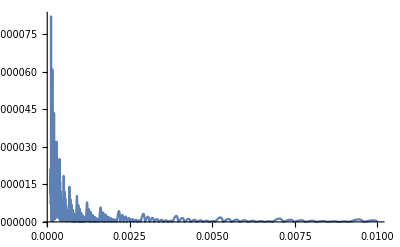

```mathematica
Plot[(-f''[x]+2m V[x]f[x]-(e-V[x])^2/4 f[x]-2m e f[x])/.sol1,{x,0.0001,0.01},PlotRange->All]
```

```mathematica
Clear[c,sol1]
```

```mathematica
e=10^-10;
sol1=First@ParametricNDSolve[{-f''[x]+2m Veff[c][x]f[x]-(e-Veff[c][x])^2/4 f[x]==2m e f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},c,AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50]
```

f→ParametricFunction[<>]

```mathematica
c/.FindRoot[(f[c]'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8m))f[c][r1])==(k+γ/r1) Cot[k r1+Realva[[1]]+γ Log[2k r1]-(l1 π)/2](*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*)/.sol1,{c,100},WorkingPrecision->30]
```

FindRoot::precw: 参数函数的精度 ((1 + 0.125` (0.0020000001`  + Times[« 2 »])) SuperscriptBox[TagBox[ParametricFunction[1, Internal`Bag[StyleBox[) 小于 WorkingPrecision (30.).

ParametricNDSolve::precw: 微分方程的精度 ({2.` (0.6349363593424098` c$323 Power[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x$324] - 1/4 (1/10000000000 + Times[« 3 »] + Times[« 3 »])^2 f[x$324] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

147.114368394813589155629883306

```mathematica
(f[c]'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8m))f[c][r1])-(k+γ/r1) Cot[k r1+Realva[[1]]+γ Log[2k r1]-(l1 π)/2]/.sol1/.c->%
```

-0.00304522

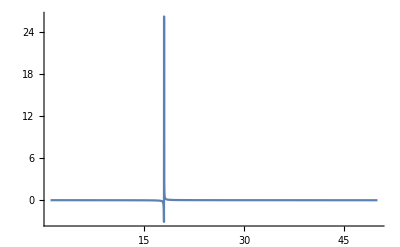

```mathematica
Plot[(f'[c][r] ((e-Veff[c][r])/(8 m)+1)-(f[c][r] Veff[c]'[r])/(8 m))/((1+(e-Veff[c][r])/(8m))f[c][r])/.c->50/.sol1,{r,1,50},PlotRange->All]
```

```mathematica
Plot[(1+(e-Veff[c][r])/(8m))f[c][r]/.c->50/.sol1,{r,0.1,50},PlotRange->All]
```

-Graphics-

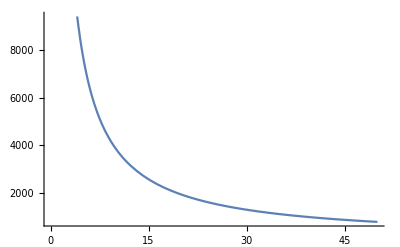

```mathematica
Plot[(k+1/(k r1)) Cot[k r1+1.0724063164215245],{r1,0,50}]
```

```mathematica
(f'[c][r1] ((e-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8m))f[c][r1])/.sol1/.c->0.1
```

0.016868

```mathematica
f'[1/10000000000][50.]/.sol1
```

ParametricNDSolve::precw: 微分方程的精度 ({2.` (0.6349363593424098` c$1089 Power[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x$1090] - 1/4 (e + Times[« 3 »] + Times[« 3 »])^2 f[x$1090] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

ParametricNDSolve::ndnum: 在 x == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

ParametricFunction[<>][1/10000000000][50.]

```mathematica
f[0.1]/.sol1
```

ParametricNDSolve::precw: 微分方程的精度 ({2.` (0.6349363593424098` c$693 Power[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x$694] - 1/4 (e + Times[« 3 »] + Times[« 3 »])^2 f[x$694] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

ParametricNDSolve::ndnum: 在 x == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

ParametricFunction[<>][0.1]

```mathematica
c=%%;
```

```mathematica
Flatten@Map[{
e=#;
sol1=First@NDSolve[{-f''[x]+2m Veff[c][x]f[x]-(e-Veff[c][x])^2/4 f[x]==2m e f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{f[r2]==u0,f'[r2]==1}}];
δs1=FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8m))f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2k r1]-(l1 π)/2](*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+δ]*)/.sol1,{δ,-0.5}]; 
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&]}&,WList]
```

NDSolve::dvnoarg: 函数 f 出现时没有参数.

Thread::tdlen: {0} 中长度不相等的对象无法合并.

ReplaceAll::reps: -1/4 f[x] (1/10000000000 + 0.1` Power[« 2 »] Erf[« 1 »] - 0.6349363593424098` Power[« 2 »] Rule[« 2 »])^2 + 2.` f[x] (-0.1` Erf[Times[« 2 »]]/x + 0.6349363593424098` ⅇ^Times[« 2 »] (f → TagBox[ParametricFunction[« 6 »], False, Rule[Editable, False], Rule[SelectWithContents, True]])) - SuperscriptBox[SuperscriptBox[f[1.`*^-8] == 1.`*^-8 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

Thread::tdlen: {0.`} 中长度不相等的对象无法合并.

General::stop: 在本次计算中，Thread :: tdlen 的进一步输出将被抑制.

ReplaceAll::reps: -0.25` f[x] (1.`*^-10 + 0.1` Power[« 2 »] Erf[« 1 »] - 0.6349363593424098` Power[« 2 »] Rule[« 2 »])^2 + 2.` f[x] (-0.1` Erf[Times[« 2 »]]/x + 0.6349363593424098` 2.718281828459045`^Times[« 2 »] (f → TagBox[ParametricFunction[« 6 »], False, Rule[Editable, False], Rule[SelectWithContents, True]])) - 1.` SuperscriptBox[SuperscriptBox[f[1.`*^-8] == 1.`*^-8 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll :: reps 的进一步输出将被抑制.

FindRoot::nlnum: 在 {δ} = {-0.5} 处，函数值 -0.125` f[50.`] (0.00004`  + Times[« 2 »] + Times[« 2 »]) + (1.`  + Times[« 2 »]) SuperscriptBox[ 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，FindRoot :: nlnum 的进一步输出将被抑制.

NDSolve::dvnoarg: 函数 f 出现时没有参数.

General::stop: 在本次计算中，NDSolve :: dvnoarg 的进一步输出将被抑制.

{δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}],δ/.FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[r1])==(k+γ/r1) Cot[k r1+δ+γ Log[2 k r1]-(l1 π)/2]/.sol1,{δ,-0.5}]}

```mathematica
Realva={0.15371513493592534,0.9244866810902964,-0.2878351571737228,0.25528639785855345,0.31741138754732695,0.3042488534914061,0.22048729085688354,0.15819049712226996,0.13705446724918247,0.09139840763169624,0.0726746912976126,0.06795477378987547};
Realva1={1.57062958127295,1.5171948969734057,0.7194917913962204,-0.017173843767820635,-0.657690842396933,-0.8971099931274864,-1.5611169827353257,1.198673864385493,1.0719675950305827,0.7990978539377087,0.6974056234372554,0.6790303670126097};
```

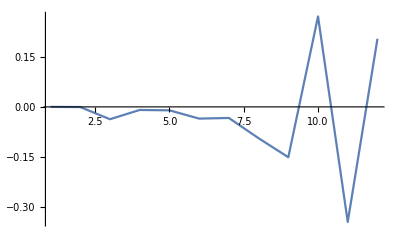

```mathematica
ListPlot[(%26-Realva)/π,Joined->True,PlotRange->All]
```

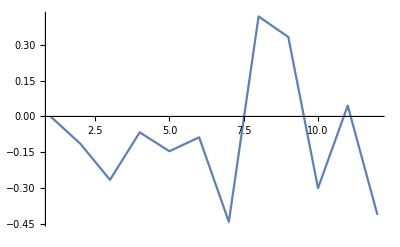

```mathematica
ListPlot[(%41-Realva)/π,Joined->True,PlotRange->All]
```

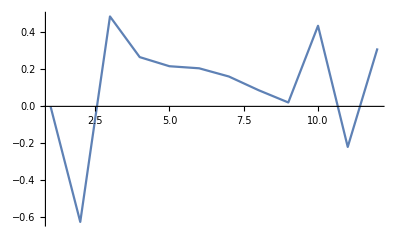

```mathematica
ListPlot[(%-Realva)/π,Joined->True,PlotRange->All](*γ/r1*)
```

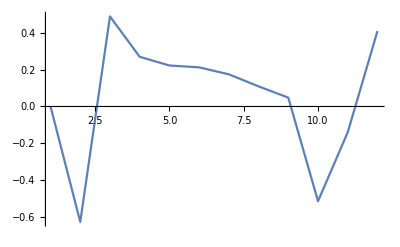

```mathematica
ListPlot[(%-Realva)/π,Joined->True,PlotRange->All]
```

```mathematica
Quit[];
```

```mathematica
e=10^-10;
sol1=First@ParametricNDSolve[{-f''[x]+2m Veff[c][x]f[x]-(e-Veff[c][x])^2/4 f[x]==2m e f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},c,AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50]
```

f→ParametricFunction[<>]

```mathematica
c/.FindRoot[(f[c]'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8m))f[c][r1])==(k+γ/r1) Cot[k r1+Realva1[[1]]](*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*)/.sol1,{c,100},WorkingPrecision->30]
```

FindRoot::precw: 参数函数的精度 ((1 + 0.125` (0.0020000001`  + Times[« 2 »])) SuperscriptBox[TagBox[ParametricFunction[1, Internal`Bag[StyleBox[) 小于 WorkingPrecision (30.).

ParametricNDSolve::precw: 微分方程的精度 ({2.` (0.6349363593424098` c$321 Power[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x$322] - 1/4 (1/10000000000 + Times[« 3 »] + Times[« 3 »])^2 f[x$322] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

139.560392853204212647393277657

```mathematica
(f[c]'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8m))f[c][r1])-(k+γ/r1) Cot[k r1+Realva1[[1]]]/.sol1/.c->139.562
```

-3.3383×10^-6

```mathematica
c=%%;
```

```mathematica
Flatten@Map[{
e=#;
sol1=First@NDSolve[{-f''[x]+2m Veff[c][x]f[x]-(e-Veff[c][x])^2/4 f[x]==2m e f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{f[r2]==u0,f'[r2]==1}}];
δs1=FindRoot[(f'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8m))f[r1])==(k+γ/r1) Cot[k r1+δ](*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+δ]*)/.sol1,{δ,-0.5}]; 
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&]}&,WList]
```

NDSolve::precw: 参数函数的精度 ({2.` (88.61196774660995` Power[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x] - 1/4 (1/10000000000 + Times[« 2 »] + Times[« 3 »])^2 f[x] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({2.` (88.61196774660995` Power[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x] - 1/4 (1/100000 + Times[« 2 »] + Times[« 3 »])^2 f[x] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({2.` (88.61196774660995` Power[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x] - 1/4 (0.001`  + Times[« 2 »] + Times[« 3 »])^2 f[x] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve :: precw 的进一步输出将被抑制.

{1.57063,1.51719,0.717445,-0.0228054,-0.673194,-0.920368,1.49171,0.92158,0.60964,-1.41757,-0.312901,1.39081}

```mathematica
Realva1
```

{1.57063,1.51719,0.719492,-0.0171738,-0.657691,-0.89711,-1.56112,1.19867,1.07197,0.799098,0.697406,0.67903}

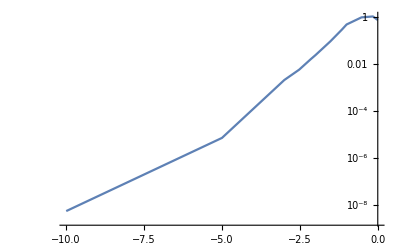

```mathematica
ListLogPlot[Transpose[{Log10@WList,Min[#]&/@Transpose[{Mod[%14-Realva1,π],π-Mod[%14-Realva1,π]}]}],Joined->True(*,PlotRange->{{0,7},{10^-3,-10^-2}}*),PlotRange->All]
```

```mathematica
Realen={0.005063846994876053,0.0012603372008835878,0.0005588472250714904,0.0003139365491734436,0.00020075015284415354,0.0001393286361501822,0.0001023202692626013,0.00007831347958375812,0.00006186146208497778,0.00005009740892103487,0.0000413957463856196,0.00003477894262660097,0.000029630516582668243,0.000025546080086868983,0.000022251441779141956,0.000019555362955836486,0.0000173211682396035,0.00001544907710193666,0.000013864867079216303,0.000012512402293718417};
```

```mathematica
Clear[e]
```

```mathematica
Realen
```

{0.00506385,0.00126034,0.000558847,0.000313937,0.00020075,0.000139329,0.00010232,0.0000783135,0.0000618615,0.0000500974,0.0000413957,0.0000347789,0.0000296305,0.0000255461,0.0000222514,0.0000195554,0.0000173212,0.0000154491,0.0000138649,0.0000125124}

```mathematica
sol2=ParametricNDSolve[{-f''[x]+2m Veff[c][x]f[x]-(e-Veff[c][x])^2/4 f[x]==2m e f[x],f'[5000]==-u0,f[5000]==u0},f,{x,5000,r2},e,WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]
```

{f→ParametricFunction[<>]}

```mathematica
FindRoot[f[e][r2]==0/.sol2,{e,-0.000012,-0.000013},PrecisionGoal->10]
```

ParametricNDSolve::precw: 微分方程的精度 ({2.` (88.61196774660995` Power[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x$10031] - 1/4 (e$10030 + Times[« 2 »] + Times[« 3 »])^2 f[x$10031] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

$Aborted